```mathematica
(*Import data from the .csv*)
```

```mathematica
s=Import["C:\\Users\\User\\Desktop\\data02.csv"];
```

```mathematica
(*Read data: Measured magnetic field (mBx,mBy,mBz) and orbital data*)
```

```mathematica
Do[mBx[i]=s[[i,1]]*10^-6,{i,1,4871}](*T*)
```

```mathematica
Do[mBy[i]=s[[i,2]]*10^-6,{i,1,4871}](*T*)
```

```mathematica
Do[mBz[i]=s[[i,3]]*10^-6,{i,1,4871}](*T*)
```

```mathematica
Do[lat[i]=s[[i,4]]*Pi/180,{i,1,4871}](*rad*)
```

```mathematica
Do[lon[i]=s[[i,5]]*Pi/180,{i,1,4871}](*rad*)
```

```mathematica
Do[alt[i]=s[[i,6]],{i,1,4871}](*m*)
```

```mathematica
(*Calculate distance to center of Earth (r)*)
```

```mathematica
a=6378137;
```

```mathematica
b=6356752.314245;
```

```mathematica
Do[r[i]=a^2/Sqrt[a^2*Cos[lat[i]]^2+b^2*Sin[lat[i]]^2] + alt[i] ,{i,1,4871}]
```

```mathematica
(*Calculate position in ECEF reference frame: X- Towards 0°N 0°E, Y- Towards 0°N 90°E, Z- Towards North*)
```

```mathematica
posx[r_,lat_,lon_]:=r*Cos[lat]*Cos[lon]
```

```mathematica
posy[r_,lat_,lon_]:=r*Cos[lat]*Sin[lon]
```

```mathematica
posz[r_,lat_,lon_]:=r*Sin[lat]
```

```mathematica
Do[x[i]=posx[r[i],lat[i],lon[i]],{i,1,4871}]
```

```mathematica
Do[y[i]=posy[r[i],lat[i],lon[i]],{i,1,4871}]
```

```mathematica
Do[z[i]=posz[r[i],lat[i],lon[i]],{i,1,4871}]
```

```mathematica
(*Calculate magnetic field (in ECEF frame)*)
```

```mathematica
m={mx,my,mz}
```

{mx,my,mz}

```mathematica
R= {Rx,Ry,Rz}
```

{Rx,Ry,Rz}

```mathematica
eBx[i_]:=10^-7*(3*(m[[1]]*(x[i]-R[[1]])+m[[2]]*(y[i]-R[[2]])+m[[3]]*(z[i]-R[[3]]))*(x[i]-R[[1]])/Sqrt[(x[i]-R[[1]])^2+(y[i]-R[[2]])^2+(z[i]-R[[3]])^2]^5-m[[1]]/Sqrt[(x[i]-R[[1]])^2+(y[i]-R[[2]])^2+(z[i]-R[[3]])^2]^3)
```

```mathematica
eBy[i_]:=10^-7*(3*(m[[1]]*(x[i]-R[[1]])+m[[2]]*(y[i]-R[[2]])+m[[3]]*(z[i]-R[[3]]))*(y[i]-R[[2]])/Sqrt[(x[i]-R[[1]])^2+(y[i]-R[[2]])^2+(z[i]-R[[3]])^2]^5-m[[2]]/Sqrt[(x[i]-R[[1]])^2+(y[i]-R[[2]])^2+(z[i]-R[[3]])^2]^3)
```

```mathematica
eBz[i_]:=10^-7*(3*(m[[1]]*(x[i]-R[[1]])+m[[2]]*(y[i]-R[[2]])+m[[3]]*(z[i]-R[[3]]))*(z[i]-R[[3]])/Sqrt[(x[i]-R[[1]])^2+(y[i]-R[[2]])^2+(z[i]-R[[3]])^2]^5-m[[3]]/Sqrt[(x[i]-R[[1]])^2+(y[i]-R[[2]])^2+(z[i]-R[[3]])^2]^3)
```

```mathematica
(*Field in ISS's reference frame*)
```

```mathematica
iBx[i_]:=((x[i]*x[i-1]+y[i]*y[i-1]+z[i]*z[i-1])*(eBx[i]*x[i]+eBy[i]*y[i]+eBz[i]*z[i])-(x[i]^2+y[i]^2+z[i]^2)*(eBx[i]*x[i-1]+eBy[i]*y[i-1]+eBz[i]*z[i-1]))/Sqrt[x[i]^2+y[i]^2+z[i]^2]/Sqrt[(y[i]*z[i-1]-z[i]*y[i-1])^2+(z[i]*x[i-1]-x[i]*z[i-1])^2+(x[i]*y[i-1]-y[i]*x[i-1])^2]
```

```mathematica
iBy[i_]:=(eBx[i]*x[i]+eBy[i]*y[i]+eBz[i]*z[i])/Sqrt[x[i]^2+y[i]^2+z[i]^2]
```

```mathematica
iBz[i_]:=(eBx[i]*(y[i]*z[i-1]-z[i]*y[i-1])+eBy[i]*(z[i]*x[i-1]-x[i]*z[i-1])+eBz[i]*(x[i]*y[i-1]-y[i]*x[i-1]))/Sqrt[(y[i]*z[i-1]-z[i]*y[i-1])^2+(z[i]*x[i-1]-x[i]*z[i-1])^2+(x[i]*y[i-1]-y[i]*x[i-1])^2]
```

```mathematica
(*Field in RaspberryPi's reference frame*)
```

```mathematica
rBx[al_,be_,ga_,i_]:=Cos[al]*Cos[be]*iBx[i]+(Cos[al]*Sin[be]*Sin[ga]-Sin[al]*Cos[ga])*iBy[i]+(Cos[al]*Sin[be]*Cos[ga]+Sin[al]*Sin[ga])*iBz[i]
```

```mathematica
rBy[al_,be_,ga_,i_]:=Sin[al]*Cos[be]*iBx[i]+(Sin[al]*Sin[be]*Sin[ga]+Cos[al]*Cos[ga])*iBy[i]+(Sin[al]*Sin[be]*Cos[ga]-Cos[al]*Sin[ga])*iBz[i]
```

```mathematica
rBz[al_,be_,ga_,i_]:=-Sin[be]*iBx[i]+Cos[be]*Sin[ga]*iBy[i]+Cos[be]*Cos[ga]*iBz[i]
```

```mathematica
(*Sum of squares of differences, which will be minimized to find the best fit*)
```

```mathematica
sq[al_,be_,ga_]:=Sum[(rBx[al,be,ga,i]-mBx[i])^2+(rBy[al,be,ga,i]-mBy[i])^2+(rBz[al,be,ga,i]-mBz[i])^2,{i,2,4871}]
```

```mathematica
NMinimize[sq[al,be,ga],{mx,my,mz,Rx,Ry,Rz,al,be,ga}]
```

{623174.,{mx→-2.86131*10^20,my→6.95022*10^22,mz→-1.44767*10^23,Rx→-6.18478*10^5,Ry→-1.30656*10^6,Rz→2.41334*10^6,al→5.42878,be→2.35411,ga→5.33624}}

```mathematica
(*Dipolar magnetic moment and its magnitude*)
```

```mathematica
m={-2.8613127162948365*10^20,6.950221000995957*10^22,-1.4476725719122252*10^23}
```

{-2.86131×10^20,6.95022×10^22,-1.44767×10^23}

```mathematica
Norm[m]
```

1.60587×10^23

```mathematica
(*Position offset and its magnitude/length*)
```

```mathematica
R= {-6.184779360517733*10^5,-1.3065567966023717*10^6,2.4133371726002335*10^6}
```

{-618478.,-1.30656×10^6,2.41334×10^6}

```mathematica
Norm[R]
```

2.81315×10^6

```mathematica
(*Error percentage function*)
```

```mathematica
al=5.428782821970854
```

5.42878

```mathematica
be=2.354105195564516
```

2.35411

```mathematica
ga=5.336235189783077
```

5.33624

```mathematica
Error= Sum[Norm[{rBx[al,be,ga,i],rBy[al,be,ga,i],rBz[al,be,ga,i]}-{mBx[i],mBy[i],mBz[i]}],{i,2,4871}]/ Sum[Norm[{mBx[i],mBy[i],mBz[i]}],{i,2,4871}]*100
```

20.1211

```mathematica
(*Magnetic field in ECEF reference frame (now in any point in space)*)
```

```mathematica
Bx[x_,y_,z_]:=10^-7*(3*(m[[1]]*(x-R[[1]])+m[[2]]*(y-R[[2]])+m[[3]]*(z-R[[3]]))*(x-R[[1]])/Sqrt[(x-R[[1]])^2+(y-R[[2]])^2+(z-R[[3]])^2]^5-m[[1]]/Sqrt[(x-R[[1]])^2+(y-R[[2]])^2+(z-R[[3]])^2]^3)
```

```mathematica
By[x_,y_,z_]:=10^-7*(3*(m[[1]]*(x-R[[1]])+m[[2]]*(y-R[[2]])+m[[3]]*(z-R[[3]]))*(y-R[[2]])/Sqrt[(x-R[[1]])^2+(y-R[[2]])^2+(z-R[[3]])^2]^5-m[[2]]/Sqrt[(x-R[[1]])^2+(y-R[[2]])^2+(z-R[[3]])^2]^3)
```

```mathematica
Bz[x_,y_,z_]:=10^-7*(3*(m[[1]]*(x-R[[1]])+m[[2]]*(y-R[[2]])+m[[3]]*(z-R[[3]]))*(z-R[[3]])/Sqrt[(x-R[[1]])^2+(y-R[[2]])^2+(z-R[[3]])^2]^5-m[[3]]/Sqrt[(x-R[[1]])^2+(y-R[[2]])^2+(z-R[[3]])^2]^3)
```

```mathematica
er=6371200
```

6371200

```mathematica
(*Calculate North magnetic pole: where the position vector and magnetic field vector are aligned*)
```

```mathematica
NMinimize[{VectorAngle[{posx[er,lat,lon],posy[er,lat,lon],posz[er,lat,lon]},{Bx[posx[er,lat,lon],posy[er,lat,lon],posz[er,lat,lon]],By[posx[er,lat,lon],posy[er,lat,lon],posz[er,lat,lon]],Bz[posx[er,lat,lon],posy[er,lat,lon],posz[er,lat,lon]]}],lat<=Pi/2,lat>=-Pi/2,lon<=Pi, lon>=-Pi},{lat,lon},Method->"RandomSearch"]
```

{0.,{lat→-0.649185,lon→3.01187}}

```mathematica
(*37.20S, 172.57E - New Zealand*)
```

```mathematica
(*Calculate South magnetic pole: where the position vector and magnetic field vector are exactly opposite*)
```

```mathematica
NMaximize[{VectorAngle[{posx[er,lat,lon],posy[er,lat,lon],posz[er,lat,lon]},{Bx[posx[er,lat,lon],posy[er,lat,lon],posz[er,lat,lon]],By[posx[er,lat,lon],posy[er,lat,lon],posz[er,lat,lon]],Bz[posx[er,lat,lon],posy[er,lat,lon],posz[er,lat,lon]]}],lat<=Pi/2,lat>=-Pi/2,lon<=Pi, lon>=-Pi},{lat,lon},Method->"RandomSearch"]
```

{3.14159,{lat→1.06683,lon→-1.89658}}

```mathematica
(*61.12N, 108.66W - North of Canada *)
```

```mathematica
(*Plot of calculated magnetic field intensity. It is in mT because the plot chooses the contours better at this scale*)
```

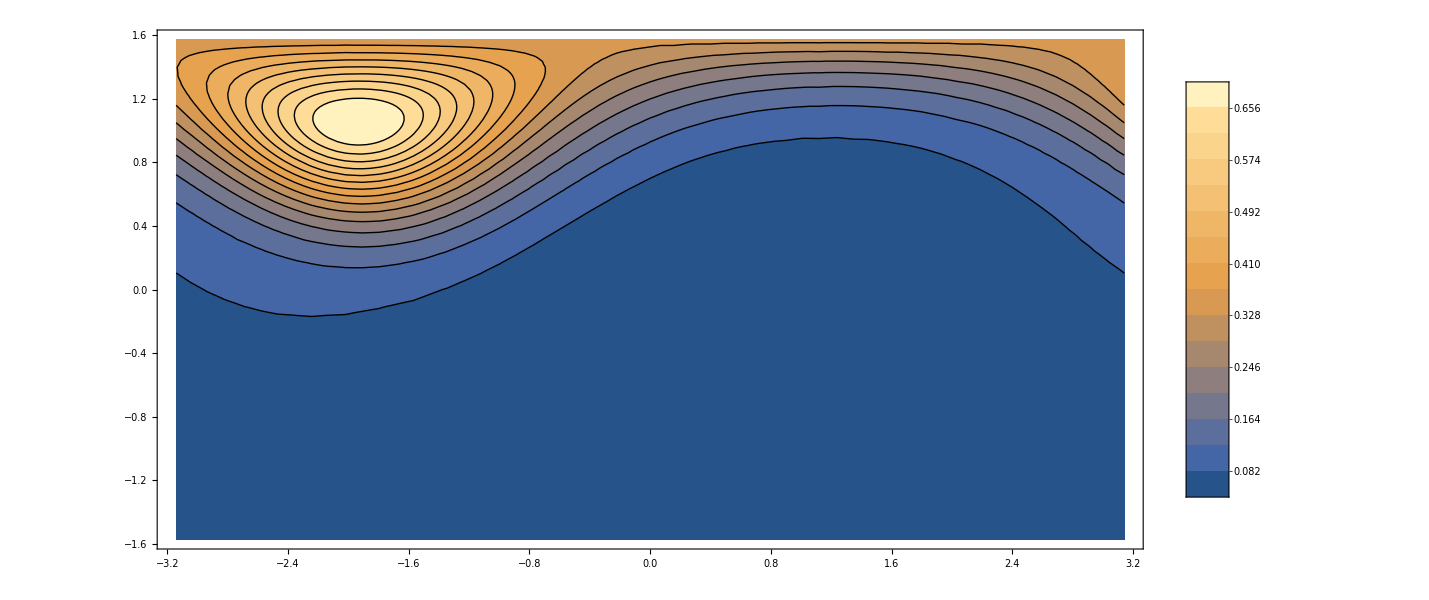

```mathematica
ContourPlot[1000*Sqrt[Bx[posx[er,lat,lon],posy[er,lat,lon],posz[er,lat,lon]]^2+By[posx[er,lat,lon],posy[er,lat,lon],posz[er,lat,lon]]^2+Bz[posx[er,lat,lon],posy[er,lat,lon],posz[er,lat,lon]]^2] ,{lon,-Pi,Pi},{lat,-Pi/2,Pi/2} ,PlotTheme->"Detailed",Contours->15,AspectRatio->1/2,PlotLegends->Placed[Automatic,After],ImageSize->1200,ContourStyle->Directive[Black,Medium,Opacity[1]]]
```